Universal Quantum Computation |

Decomposition into Two-Level Unitary Matricespaclet:Q3/tutorial/UniversalQuantumComputation#1255432361 | Implementation of Two-Level Unitary Matrices: Gray Code Sequencepaclet:Q3/tutorial/UniversalQuantumComputation#1829642645
Implementation of Two-Level Unitary Matrices: Ideapaclet:Q3/tutorial/UniversalQuantumComputation#1012467270 | Universal Quantum Computation Theorempaclet:Q3/tutorial/UniversalQuantumComputation#205503201

See also Section 2.4 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

In classical computation, it is known that a finite set of logic gates—typically including AND, OR, and NOT—is sufficient to calculate any binary function. The set is said to be universal for classical computation. Does there exist a universal set of elementary quantum logic gates for quantum computation that enables to implement any arbitrary quantum unitary operation?

TwoLevelDecompositionpaclet:Q3/ref/TwoLevelDecompositionQ3 Package Symbol | Decomposes a unitary operator into a list of two-level unitary operators
TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol | Represents a two-level unitary operator
FromTwoLevelUpaclet:Q3/ref/FromTwoLevelUQ3 Package Symbol | Rewrites a two-level unitary operator in terms of CNOT and controlled-unitary gates

Q3 functions related to the universal quantum computation theorem.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Decomposition into Two-Level Unitary Matrices

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Suppose that we want to implement an arbitrary unitary operation U on an n-qubit register. We start by decomposing U into a set of two-level unitary transformations T_k, that is,

U=T_L⋯ T_2 T_1 .

The procedure is detailed for arbitrary two-qubit unitary gates in Two-Qubit Gates. To summarize the procedure, first  remove the off-diagonal element U_(1 n) at the top-right corner of the matrix representation of U by multiplying U with a two-level unitary transformation T_1^† on the right, and repeat it along the top row and then the next consecutive rows to zero all off-diagonal elements and to set every diagonal element to unity, so that

U T_1^†T_2^†⋯ T_L^†=I .

The decomposition of U is then given by

U=T_L⋯ T_2 T_1 .

as desired.

For demonstration, consider a three-qubit system, and an arbitrary unitary operation on it.

```mathematica
$n=3;
SS=S[Range[$n],None];
mat=RandomUnitary[2^$n];
mat[[;;3,;;3]]//MatrixForm
```

(0.202074+0.548057 ⅈ | -0.32978+0.17648 ⅈ | 0.131188-0.0428045 ⅈ
-0.127542+0.477552 ⅈ | 0.611596+0.113158 ⅈ | -0.11799+0.0134002 ⅈ
0.0683769-0.0203506 ⅈ | -0.00267641-0.243863 ⅈ | 0.622256+0.336675 ⅈ)

```mathematica
op=ExpressionFor[mat,SS];
qc=QuantumCircuit[{op,"Label"->"U"}]
```

-Graphics-

```mathematica
twl=TwoLevelDecomposition[mat];
```

```mathematica
MatrixForm/@Matrix/@twl[[;;3]]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.+0. ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.315507-0.948923 ⅈ),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.529606+0.778263 ⅈ | 0.223172-0.25302 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -0.223172-0.25302 ⅈ | 0.529606-0.778263 ⅈ),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.423549-0.214833 ⅈ | 0.88003 | 0
0 | 0 | 0 | 0 | 0 | -0.88003 | 0.423549+0.214833 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Implementation of Two-Level Unitary Matrices: Idea

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Some two-level unitary transformations are themselves multi-control unitary gates, which can be implemented in terms of elementary gates. The most common example is

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⋱ | ⋮ | ⋮
0 | 0 | ⋯ | U_11 | U_12
0 | 0 | ⋯ | U_21 | U_22) .

On three qubits, another example is

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | ⋱ | ⋮ | ⋮ | ⋮
0 | 0 | ⋯ | V_11 | 0 | V_12
0 | 0 | ⋯ | 0 | 1 | 0
0 | 0 | ⋯ | V_21 | 0 | V_22)     ≐ ,

where the gate with label ‘V ’ on the second qubit indicates unitary operator

V≐(V_11 | V_12
V_21 | V_22) .

Some other two-level unitary transformations are not multi-control unitary gates and yet simple variants. An example is

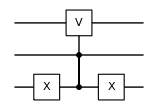
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | V_11 | 0 | 0 | 0 | V_12 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | V_21 | 0 | 0 | 0 | V_22 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)     ≐ -Graphics-,

In this case, unitary operator V acts conditioned on the second qubit in |1⟩ and the third qubit in |0⟩ (rather than |1⟩), and the above two-level unitary transformation is a simple variant of multi-control unitary gate.

Through these examples, we see that any two-level unitary gate with the two non-trivial columns and rows attributed to two logical basis states differing only in one qubit is either a multi- control unitary gate or a simple variant of it. It is thus clear that such a two-level unitary transformation can be implemented in terms of elementary gates.

Two-level unitary transformations that do not belong to the above class requires additional manipulation. The basic idea is to simultaneously exchange columns and rows so that the resulting matrix corresponds to a controlled-unitary gate such as the one seen above. Furthermore, a series of simultaneous exchanges of columns and rows bring any two-level unitary transformation to a multi-control unitary gate and that each exchange of columns of rows can be carried by the multi-control NOT gate or a simple variant of it.

For example, consider a two-level unitary transformation T on three qubits of the following form,

T≐(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | V_11 | V_12 | 0
0 | 0 | 0 | 0 | 0 | V_21 | V_22 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)  .

The simultaneous exchange of the last two columns and rows brings the above two-level unitary matrix to the form seen at the beginning. On the other hand, given that the last two columns (or rows) in the matrix representation correspond to the logical basis states |110⟩ and |111⟩, respectively, the simultaneous exchange of the last two columns and rows can be carried out by the multi-control NOT gate with the first two qubits as controls and the third qubit as target. Putting these two observations together, we find that

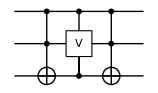
T= -Graphics-.

For demonstration, consider one of the two above examples.

```mathematica
<<Q3`
Let[Qubit,S]
```

A two-level unitary matrix is represented in a compact way by TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol.

```mathematica
opT=TwoLevelU[Normal@TheRotation[Pi/3,2],{6,7},8]
```

TwoLevelU[{{(√3)/2,-1/2},{1/2,(√3)/2}},{6,7},8]

Here is the conventional form of the above two-level unitary matrix.

```mathematica
mat=Matrix@opT;
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

We want to exchange the last two columns and rows simultaneously. This may be achieved by using the corresponding permutation matrix, which happens to be equivalent to the matrix representation of the CNOT gate in this case.

```mathematica
P=Matrix[CNOT[S@{1,2},S[3]]];
P//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

Here is the resulting matrix after the simultaneous exchange of the last two columns and rows.

```mathematica
new=P.mat.Topple[P];
new//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | (√3)/2)

The above matrix is nothing but a multi-control unitary operator with the first and third as the control qubits.

```mathematica
op=ControlledU[S@{1,3},Rotation[Pi/3,S[2,2]]];
Normal@Matrix[op]//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | (√3)/2)

In summary, the two-level unitary matrix is equivalent to the following quantum circuit.

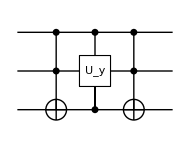

```mathematica
qc=QuantumCircuit[CNOT[S@{1,2},S[3]],op,CNOT[S@{1,2},S[3]]]
```

```mathematica
Matrix[qc]-mat//Normal//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Implementation of Two-Level Unitary Matrices: Gray Code Sequence

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

So far, the exchanges of columns and rows have been performed on an ad hoc basis. An irritating issue is that every exchange of columns or rows cannot be carried out by a single multi-control NOT gate or a simple variant of it. Fortunately, however, one can achieve any desired exchange by combining a sequence of other exchanges that can be carried out by a multi-control NOT gate (or a simple variant).

For example, suppose that we want to exchange the sixth and seventh columns and rows. Noting that these columns and rows in the matrix representation correspond to logical basis states |101⟩ and |110⟩, it is clear that the exchange cannot be fulfilled by a single multi-control NOT gate. However, it can be achieved by first exchanging the sixth and eighth columns and rows (respectively corresponding to logical basis states |101⟩ and |111⟩) and then the eighth and seventh columns and rows (respectively corresponding to |111⟩ and |110⟩). The first exchange can be carried out by the multi-control NOT gate with the first and third qubit as controls and the second qubit as target while the second exchange can be implemented by the multi-control NOT gate with the first two qubits as controls and the third qubit as target.

The key point is that each exchange must be between a pair of columns (and rows) corresponding to logical basis states that differ in only one qubit. For this purpose, a systematic and efficient way is to use the Gray code sequence. In terms of classical bits, it is a sequence of bit strings where any two successive strings are different only in one bit. As an example, the Gray code sequence from |010⟩ to |101⟩ is given by

010→110→111→101.

The first step in the above sequence corresponds to the NOT gate on the first qubit conditioned on the second qubit in |1⟩ and the third qubit in |0⟩, which is a simple variant of the multi-control NOT gate with the last two qubits as control and the first qubit as target—it just needs additional NOT gates on the third qubit before and after the multi-control NOT gate. The other steps can be carried out simply by multi-control NOT gates.

For demonstration, let us consider a particular two-level unitary matrix on a three-qubit system. We want to implement it in terms of elementary quantum logic gates.

```mathematica
U=TheRotation[Pi/3,2];
U//MatrixForm
```

((√3)/2 | -1/2
1/2 | (√3)/2)

```mathematica
$n=3;
SS=S[Range[$n],None];
mat=Matrix@TwoLevelU[U,{4,5},2^$n];
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
op=ExpressionFor[mat,SS]
```

1/8 (6+√3)+1/8 (2-√3) S_1^z S_2^z+1/8 (2-√3) S_1^z S_3^z+1/8 (-2+√3) S_2^z S_3^z-1/2 S_1^+S_2^-S_3^-+1/2 S_1^-S_2^+S_3^+

Our implementation is based on the Gray code sequence. Notice the function Reverse.

```mathematica
gates=Flatten@FromTwoLevelU[U,{4,5},SS]
```

{S_1^x,CNOT[{S_1,S_2},{S_3}],S_1^x,S_3^x,CNOT[{S_2,S_3},{S_1}],S_3^x,CNOT[{S_1,S_2},{S_3}],CNOT[{S_1,S_3},{S_2}],S_2^x,ControlledU[{S_1,S_2},(√3)/2+(ⅈ S_3^y)/2,Label→U],S_2^x,CNOT[{S_1,S_3},{S_2}],CNOT[{S_1,S_2},{S_3}],S_3^x,CNOT[{S_2,S_3},{S_1}],S_3^x,S_1^x,CNOT[{S_1,S_2},{S_3}],S_1^x}

```mathematica
new=Apply[Dot,Matrix[#,SS]&/@Elaborate/@gates]//Normal//Simplify;
new//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

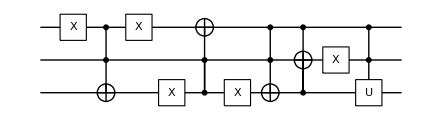

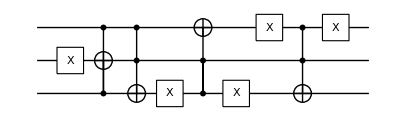

```mathematica
qc1=QuantumCircuit@@gates[[;;10]]
qc2=QuantumCircuit@@gates[[11;;]]
```

```mathematica
new=Matrix[qc2].Matrix[qc1]//Normal//Simplify;
new//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

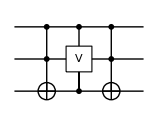

```mathematica
QuantumCircuit[CNOT[S@{1,2},S[3]],ControlledU[S@{1,3},S[2,1],"Label"->"V"],CNOT[S@{1,2},S[3]],
"PortSize"->0.2]
```

Universal Quantum Computation Theorem

We have seen that one can implement any unitary operation combining the CNOT and single-qubit gates.

A subtle issue is that single-qubit gates form a continuum of unitary operators. It is impractical to implement them to an infinite accuracy. Fortunately, it is known that a discrete set of gates is sufficient to perform universal quantum computation. The Hadamard, quadrant phase, octant phase, and CNOT gates form a universal set of gates in the sense that an arbitrary gate on n qubits can be approximated to arbitrary accuracy using a quantum circuit composed of only such gates.

The quadrant phase gate is equal to the square of the octant phase, and it may sound redundant to include the quadrant phase. In the context of the universal set of elementary gates alone, it is certainly true. However, the quadrant phase gate is typically included in the universal set because it is required to fault-tolerantly implement the octant phase.

It is also interesting to note that the set remains universal if octant phase gates are replaced with Toffoli gates.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Universal Quantum Computation: Demonstration
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).